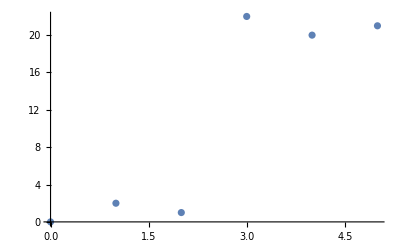

```mathematica
ListPlot[{{0,0},{1,2},{2,1},{3,22},{4,20},{5,21}}]
```

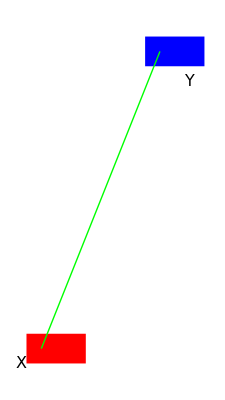

```mathematica
Graphics[{Red,Rectangle[{0,0},{2,1}],Blue,Rectangle[{4,10},{6,11}],Green,Line[{{0.5,0.5},{4.5,10.5}}] ,Black,Text[StyleForm["X",FontSize->16],{-0.2,0}],Text[StyleForm["Y",FontSize->16],{5.5,9.5}] }]
```

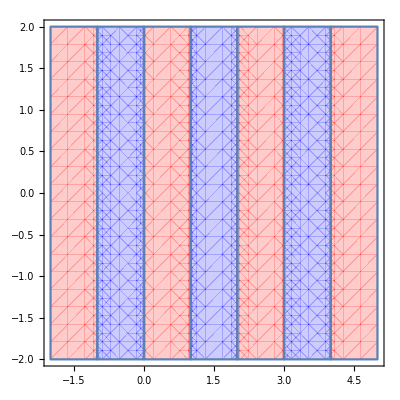

```mathematica
Show[RegionPlot[{Mod[Floor[x],2]==0},{x,-2,5},{y,-2,2}, PlotStyle->{Opacity[0.2],Red},Axes->True],RegionPlot[{Mod[Floor[x],2]==1},{x,-2,5},{y,-2,2}, PlotStyle->{Opacity[0.2],Blue}]]
```